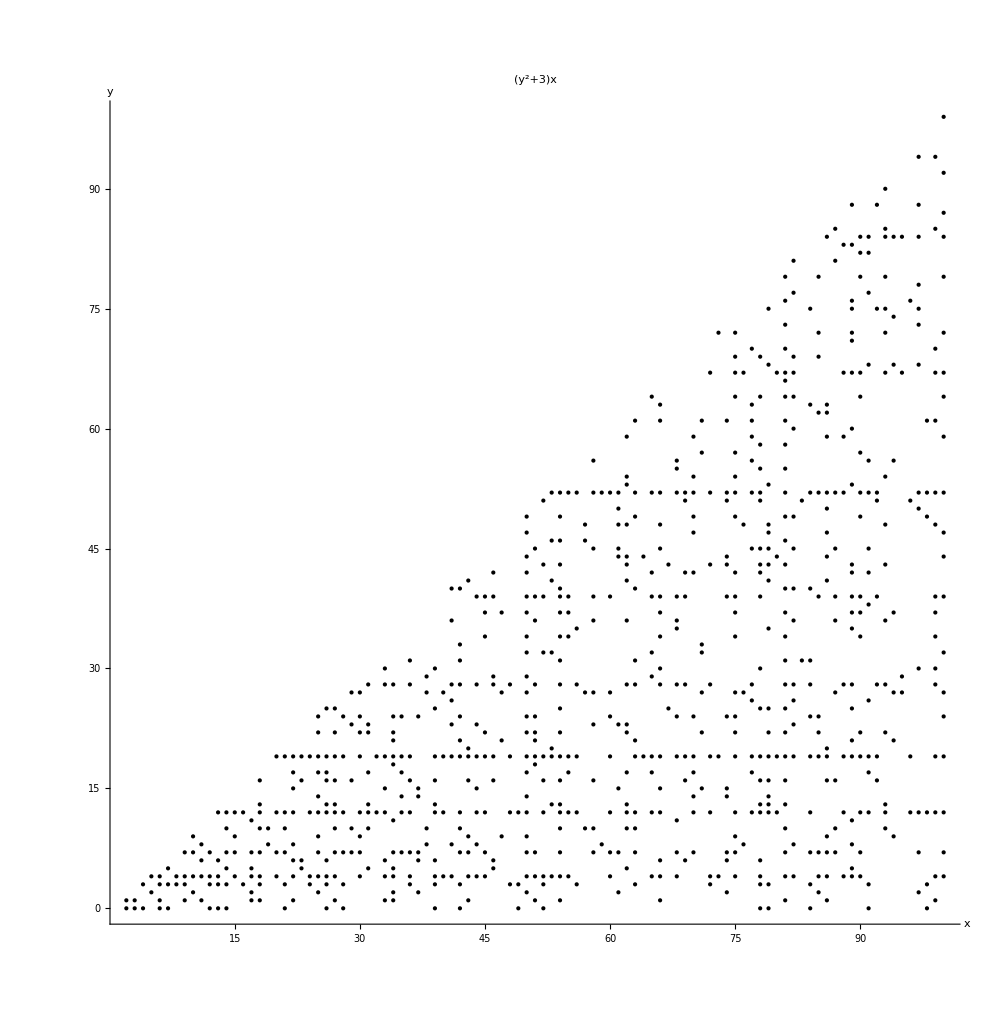

```mathematica
φ[y_]:=y^2+3;
maxmod=100;

per={};spp={};pspp={};pper={};ptper={};
For[mod=2,mod≤maxmod,mod++,
f[x_]:=Mod[φ[x],mod];
For[n=0,n≤mod-1,n++,If[Count[Mod[NestList[f,n,mod],mod],n]>1,AppendTo[per,n]]];pper=Flatten[Join[{mod,Riffle[per,mod]}]];ptper=Flatten[Join[pper,ptper]];per={};];Graphics[Point[Partition[ptper,2]],Axes->True,AxesLabel->{x,y},ImageSize->1000,PlotLabel->Mod[φ[y],x]]
```